```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/化学实验报告/figures"];
<<MaTeX`;
```

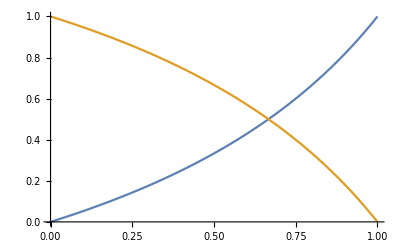

```mathematica
Plot[{(x*1)/(x*(1-2)+2),1-(x*1)/(x*(1-2)+2)},{x,0,1}]
```

```mathematica
ToExpression["\\frac{x_Ap_A^*}{p_B^*+(p_A^*-p_B^*)x_A}",TeXForm]
```

(x_A (p_A)^*)/(x_A ((p_A)^*-(p_B)^*)+(p_B)^*)

```mathematica
Integrate[Sqrt[r^2-x^2],{x,a,r}]
```

Integrate::idiv: Integral of √(r^2-x^2) does not converge on {a,r}.

∫_a^r √(r^2-x^2)ⅆx

```mathematica
Solve[%==0,C[1]]
```

{}

```mathematica
DSolve[(2 L1 q)/(1+x[t]/r)==x'[t],x[t],t]
```

{{x[t]→-r-√(r^2+4 L1 q r t+2 C[1])},{x[t]→-r+√(r^2+4 L1 q r t+2 C[1])}}

```mathematica
Solve[(-r+√(r^2+4 L1 q r t+2 C[1])/.t->0)==0,C[1]]
```

{{C[1]→0}}

```mathematica
%25/.{q->σ,L1->Subscript[L, 1],C[1]->c}
```

{{x[t]→-r-√(2 c+r^2+4 r t σ L_1)},{x[t]→-r+√(2 c+r^2+4 r t σ L_1)}}

```mathematica
-r-√(2 c+r^2+4 r t σ Subscript[L, 1])//TeXForm
```

-\sqrt{2 c+4 L_1 r \sigma  t+r^2}-r

```mathematica
2 Pi (r^2-(-r+√(r^2+4 L1 q r t))^2)D[-r+√(r^2+4 L1 q r t),t]
```

(4 L1 π q r (r^2-(-r+√(r^2+4 L1 q r t))^2))/(√(r^2+4 L1 q r t))

```mathematica
Integrate[%,{t,0,a}]
```

$Aborted

```mathematica
(4 L1 π q r (r^2-(-r+√(r^2+4 L1 q r t))^2))/(√(r^2+4 L1 q r t))/.{q->σ,L1->Subscript[L, 1],C[1]->c}//TeXForm
```

\frac{4 \pi  L_1 r \sigma  \left(r^2-\left(\sqrt{4 L_1 r \sigma 
   t+r^2}-r\right){}^2\right)}{\sqrt{4 L_1 r \sigma  t+r^2}}

```mathematica
(4 L1 π q r (r^2-(-r+√(r^2+4 L1 q r t))^2))/(√(r^2+4 L1 q r t))/.{q->σ,L1->Subscript[L, 1],C[1]->c}
```

(4 π r σ L_1 (r^2-(-r+√(r^2+4 r t σ L_1))^2))/(√(r^2+4 r t σ L_1))

```mathematica
(4 L1 π q r (r^2-(-r+√(r^2+4 L1 q r t))^2))/(√(r^2+4 L1 q r t))/.{q->1,r->1,L1->1}
```

(4 π (1-(-1+√(1+4 t))^2))/(√(1+4 t))

```mathematica
"HeatAbsorption.eps"~Export~Plot[%40,{t,0,3/4},AxesLabel->MaTeX/@{t,dn/dt}]
```

HeatAbsorption.eps

```mathematica
-r+√(r^2+4 L1 q r t+2 C[1])/.{r->1,L1->1,q->1,C[1]->0}
```

-1+√(1+4 t)

```mathematica
Solve[%50==1,t]
```

{{t→3/4}}

```mathematica
DSolve[D[D[T[x,y],x],x]+D[D[T[x,y],y],y]==0,T[x,y],{x,y}]
```

{{T[x,y]→C[1][ⅈ x+y]+C[2][-ⅈ x+y]}}

```mathematica
D[D[C[1][ⅈ x+y]+C[2][-ⅈ x+y],x],x]
```

-C[1]''[ⅈ x+y]-C[2]''[-ⅈ x+y]

```mathematica
D[D[C[1][ⅈ x+y]+C[2][-ⅈ x+y],y],y]
```

C[1]''[ⅈ x+y]+C[2]''[-ⅈ x+y]

```mathematica
27.0/30.50
```

0.885246

```mathematica
StringJoin@@Table[StringJoin["\\fancyput*(-0.1cm,",ToString@i,"cm){\\tiny $|$}\n"],{i,-19.8,-30,-0.4}]
```

\fancyput*(-0.1cm,-19.8cm){\tiny $|$}
\fancyput*(-0.1cm,-20.2cm){\tiny $|$}
\fancyput*(-0.1cm,-20.6cm){\tiny $|$}
\fancyput*(-0.1cm,-21.cm){\tiny $|$}
\fancyput*(-0.1cm,-21.4cm){\tiny $|$}
\fancyput*(-0.1cm,-21.8cm){\tiny $|$}
\fancyput*(-0.1cm,-22.2cm){\tiny $|$}
\fancyput*(-0.1cm,-22.6cm){\tiny $|$}
\fancyput*(-0.1cm,-23.cm){\tiny $|$}
\fancyput*(-0.1cm,-23.4cm){\tiny $|$}
\fancyput*(-0.1cm,-23.8cm){\tiny $|$}
\fancyput*(-0.1cm,-24.2cm){\tiny $|$}
\fancyput*(-0.1cm,-24.6cm){\tiny $|$}
\fancyput*(-0.1cm,-25.cm){\tiny $|$}
\fancyput*(-0.1cm,-25.4cm){\tiny $|$}
\fancyput*(-0.1cm,-25.8cm){\tiny $|$}
\fancyput*(-0.1cm,-26.2cm){\tiny $|$}
\fancyput*(-0.1cm,-26.6cm){\tiny $|$}
\fancyput*(-0.1cm,-27.cm){\tiny $|$}
\fancyput*(-0.1cm,-27.4cm){\tiny $|$}
\fancyput*(-0.1cm,-27.8cm){\tiny $|$}
\fancyput*(-0.1cm,-28.2cm){\tiny $|$}
\fancyput*(-0.1cm,-28.6cm){\tiny $|$}
\fancyput*(-0.1cm,-29.cm){\tiny $|$}
\fancyput*(-0.1cm,-29.4cm){\tiny $|$}
\fancyput*(-0.1cm,-29.8cm){\tiny $|$}

```mathematica
"\fancyput(-0.1cm,-9.3cm){\tiny $|$}"
```

```mathematica
Solve[{SparseArray[{Band[{1,1}]->x,Band[{2,1}]->1,Band[{1,2}]->1},{3,3}].{c1,c2,c3}=={0,0,0},c1==c2==c3},{c1,c2,c3}]
```

{{c1→0,c2→0,c3→0}}

```mathematica
Solve[SparseArray[{Band[{1,1}]->α-e,Band[{2,1}]->β,Band[{1,2}]->β},{3,3}].{c1,c2,c3}=={0,0,0},{α,β}]
```

{{α→e,β→0}}

```mathematica
SparseArray[{Band[{1,1}]->α-e,Band[{2,1}]->β,Band[{1,2}]->β},{3,3}].{c1,c2,c3}
```

{c1 (-e+α)+c2 β,c2 (-e+α)+c1 β+c3 β,c3 (-e+α)+c2 β}

```mathematica
Solve[{SparseArray[{Band[{1,1}]->x,Band[{2,1}]->1,Band[{1,2}]->1,Band[{3,1}]->1,Band[{1,3}]->1},{3,3}].{c1,c2,c3}=={0,0,0}}/.{c2->c1,c3->c1},x]
```

{{x→-2}}

```mathematica
Solve[SparseArray[{Band[{1,1}]->x,Band[{2,1}]->1,Band[{1,2}]->1},{3,3}].{c1,c2,c3}=={0,0,0},e]
```

{}

```mathematica
{SparseArray[{Band[{1,1}]->x,Band[{2,1}]->1,Band[{1,2}]->1,Band[{3,1}]->1,Band[{1,3}]->1},{3,3}].{c1,c2,c3}=={0,0,0}}/.{c2->c1,c3->c1}
```

{{2 c1+c1 x,2 c1+c1 x,2 c1+c1 x}=={0,0,0}}

```mathematica
Solve[{SparseArray[{Band[{1,1}]->x,Band[{2,1}]->1,Band[{1,2}]->1,Band[{3,1}]->1,Band[{1,3}]->1},{3,3}].{c1,c2,c3}=={0,0,0},c1==c2,c2==c3},x]
```

{}

```mathematica
Reduce[{SparseArray[{Band[{1,1}]->x,Band[{2,1}]->1,Band[{1,2}]->1,Band[{3,1}]->1,Band[{1,3}]->1},{3,3}].{c1,c2,c3}=={0,0,0},c2==c3,c1^2+c2^2+c3^2==1},x]
```

(c3==-1/(√3)||c3==1/(√3)||c3==-1/(√6)||c3==1/(√6))&&c2==c3&&c1==c3 (-5+18 c3^2)&&x==-2 (-2+9 c3^2)

```mathematica
Reduce[{SparseArray[{Band[{1,1}]->x,Band[{2,1}]->1,Band[{1,2}]->1},{3,3}].{c1,c2,c3}=={0,0,0},c1==c3,c1^2+c2^2+c3^2==1},x]
```

(c3==-1/2||c3==1/2)&&(c2==-1/(√2)||c2==1/(√2))&&c1==c3&&x==-4 c2 c3

```mathematica
Reduce[{SparseArray[{Band[{1,1}]->x,Band[{2,1}]->1,Band[{1,2}]->1},{3,3}].{c1,c2,c3}=={0,0,0},c1==-c3,c1^2+c2^2+c3^2==1},x]
```

(c3==-1/(√2)||c3==1/(√2))&&c2==0&&c1==-c3&&x==0

```mathematica
Reduce[{SparseArray[{Band[{1,1}]->x,Band[{2,1}]->1,Band[{1,2}]->1},{3,3}].{c1,c2,c3}=={0,0,0},c1==c2,c1^2+c2^2+c3^2==1},x]
```

False